```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]
```

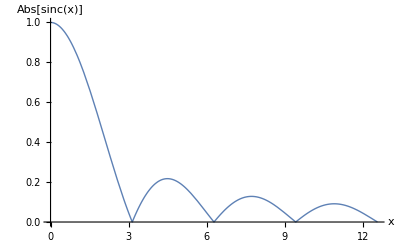

```mathematica
modernOpticsMidtermReflectionFig8 = Plot[
Abs[Sinc[x]], {x, 0, 4 Pi}
, AxesLabel->{x, Style[Abs[Sinc[x]], FontSize-> 14]}
, PlotRange->Full
, PlotStyle-> Thick
]

(* 
http://mathematica.stackexchange.com/questions/15929/how-to-make-the-file-size-for-mathematica-9-export-graphic-smaller-like-mathema *)

(*too big*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\foo9.pdf", %]*)

(*okay*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\foo9.pdf",First[ImportString[ExportString[%,"PDF"],"PDF"]]]*)
```

```mathematica
peeters`exportForLatex["modernOpticsMidtermReflectionFig8",modernOpticsMidtermReflectionFig8]
```

{modernOpticsMidtermReflectionFig8.eps,modernOpticsMidtermReflectionFig8pn.png}